# QED calculation: Peskin Sec. 5

## e^-e^+→γ γ : Peskin P.153-54

-Graphics-

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.9 (23 Sep 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (21 Feb 2018)

by Thomas Hahn

### Create Topology & Insert Particles

loading generic model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counter terms of order 1

> 6 counter terms of order 2

classes model {SM} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 2 Classes insertions

> Top. 1: 1 diagram

> Top. 2: 1 diagram

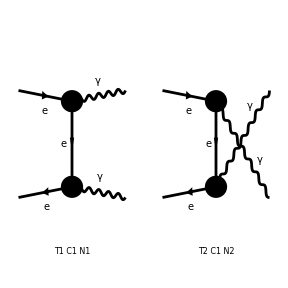

```mathematica
topologies=CreateTopologies[0,2->2];
diagrams=InsertFields[topologies,{F[2,{1}],-F[2,{1}]}->{V[1],V[1]},InsertionLevel->{Classes}];
Paint[diagrams];
```

### Pass the diagram to FormCalc

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

in total: 2 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{V[1],k[3],0,{}},{V[1],k[4],0,{}}}][-Alfa π (8 Pair3 Den[T,ME2]-8 Pair4 Den[U,ME2]) Mat[F1]-Alfa Pair1 π (4 Den[T,ME2]-4 Den[U,ME2]) Mat[F2]-4 Alfa π (Den[T,ME2]+Den[U,ME2]) Mat[F3]+Alfa Pair2 π (4 Den[T,ME2]-4 Den[U,ME2]) Mat[F4]]

Take an average for initial fermions

```mathematica
_Hel=0;
squared=SquaredME[amplitude]
helSquared=squared[[1]]//.squared[[2]]//.HelicityME[amplitude]
(* Or, you may want to use a shorter but less comprehensive command:
helSquared = SquaredME[amplitude] // (#[[1]]//.#[[2]])& //. HelicityME[amplitude] *)
```

{FF[F1] (FFC[F1] Mat[F1,F1]+FFC[F2] Mat[F1,F2]+FFC[F3] Mat[F1,F3]+FFC[F4] Mat[F1,F4])+FF[F2] (FFC[F1] Mat[F2,F1]+FFC[F2] Mat[F2,F2]+FFC[F3] Mat[F2,F3]+FFC[F4] Mat[F2,F4])+FF[F3] (FFC[F1] Mat[F3,F1]+FFC[F2] Mat[F3,F2]+FFC[F3] Mat[F3,F3]+FFC[F4] Mat[F3,F4])+FF[F4] (FFC[F1] Mat[F4,F1]+FFC[F2] Mat[F4,F2]+FFC[F3] Mat[F4,F3]+FFC[F4] Mat[F4,F4]),{FF[F1]→-Alfa π (8 Pair3 Den[T,ME2]-8 Pair4 Den[U,ME2]),FF[F2]→-Alfa Pair1 π (4 Den[T,ME2]-4 Den[U,ME2]),FF[F3]→-4 Alfa π (Den[T,ME2]+Den[U,ME2]),FF[F4]→Alfa Pair2 π (4 Den[T,ME2]-4 Den[U,ME2]),FFC[F1]→-Alfa π (8 Pair3^* Den[T,ME2]-8 Pair4^* Den[U,ME2]),FFC[F2]→-Alfa π Pair1^* (4 Den[T,ME2]-4 Den[U,ME2]),FFC[F3]→-4 Alfa π (Den[T,ME2]+Den[U,ME2]),FFC[F4]→Alfa π Pair2^* (4 Den[T,ME2]-4 Den[U,ME2])}}

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

-4 Alfa π (Den[T,ME2]+Den[U,ME2]) (1/2 Abb11 Alfa Pair2 π Pair1^* (4 Den[T,ME2]-4 Den[U,ME2])-1/2 Abb13 Alfa π Pair2^* (4 Den[T,ME2]-4 Den[U,ME2])-2 Alfa (-Abb18-2 ME2 Pair12 Pair2) π (Den[T,ME2]+Den[U,ME2])+1/2 Abb15 Alfa π (8 Pair3^* Den[T,ME2]-8 Pair4^* Den[U,ME2]))-Alfa π (8 Pair3 Den[T,ME2]-8 Pair4 Den[U,ME2]) (-1/2 Alfa (-Abb4-2 ME2 Pair2) π Pair1^* (4 Den[T,ME2]-4 Den[U,ME2])+1/2 Alfa (-Abb2-2 ME2 Pair5) π Pair2^* (4 Den[T,ME2]-4 Den[U,ME2])+2 Abb7 Alfa π (Den[T,ME2]+Den[U,ME2])-1/2 Alfa (Abb3+2 ME2) π (8 Pair3^* Den[T,ME2]-8 Pair4^* Den[U,ME2]))-Alfa Pair1 π (4 Den[T,ME2]-4 Den[U,ME2]) (-1/2 Alfa π (ME2-T) (ME2-U) Pair1^* (4 Den[T,ME2]-4 Den[U,ME2])-1/2 Abb8 Alfa π Pair2^* (4 Den[T,ME2]-4 Den[U,ME2])+2 Abb10 Alfa Pair12 π (Den[T,ME2]+Den[U,ME2])-1/2 Alfa (-Abb9-2 ME2 Pair12) π (8 Pair3^* Den[T,ME2]-8 Pair4^* Den[U,ME2]))+Alfa Pair2 π (4 Den[T,ME2]-4 Den[U,ME2]) (1/2 Abb17 Alfa π Pair1^* (4 Den[T,ME2]-4 Den[U,ME2])+1/2 Alfa (Abb19+2 ME2) π Pair2^* (4 Den[T,ME2]-4 Den[U,ME2])+2 Abb22 Alfa π (Den[T,ME2]+Den[U,ME2])-1/2 Alfa (-Abb21-2 ME2 Pair13) π (8 Pair3^* Den[T,ME2]-8 Pair4^* Den[U,ME2]))

What are these abbreviations?

```mathematica
Abbr[]
Subexpr[]
```

{F4→<v1|1,ec[3]|u2>,F1→<v1|1,ec[4]|u2>,F2→<v1|1,k[3]|u2>,F3→<v1|-1,ec[3],ec[4],k[3]|u2>,Pair5→Pair[e[3],ec[4]],Pair8→Pair[e[3],k[1]],Pair6→Pair[e[3],k[2]],Pair13→Pair[e[4],ec[3]],Pair11→Pair[e[4],k[1]],Pair10→Pair[e[4],k[2]],Pair12→Pair[e[4],k[3]],Pair1→Pair[ec[3],ec[4]],Pair3→Pair[ec[3],k[1]],Pair4→Pair[ec[3],k[2]],Pair7→Pair[ec[4],k[1]],Pair9→Pair[ec[4],k[2]],Pair2→Pair[ec[4],k[3]],Abb22→Abb6+Abb10 Pair13,Abb15→Abb14-Abb12 Pair13,Abb20→Pair10 Pair3+Pair11 Pair4,Abb13→Abb12+Abb11 Pair5,Abb7→Abb5-Abb6 Pair5,Abb1→Pair6 Pair7+Pair8 Pair9,Abb19→-2 ME2+2 Pair3 Pair6+2 Pair4 Pair8+S,Abb3→-2 ME2+2 Pair10 Pair7+2 Pair11 Pair9+S,Abb21→-2 Abb20+Pair13 (-2 ME2+S),Abb2→-2 Abb1+Pair5 (-2 ME2+S),Abb18→-Abb16+Abb8 Pair13 Pair2+Pair5 (Abb17 Pair12+Pair13 (ME2-T) (ME2-U)),Abb5→Pair6 (-ME2-2 Pair11 Pair2+T)+Pair8 (ME2+2 Pair10 Pair2-U),Abb14→Pair4 (-ME2-2 Pair12 Pair7+T)+Pair3 (ME2+2 Pair12 Pair9-U),Abb16→Pair12 (Pair2 (4 ME2-2 Pair3 Pair6-2 Pair4 Pair8-S-2 T)+Pair7 (T-U))+(ME2-T) (ME2-U)+Pair11 Pair2 (T-U),Abb6→Pair10 (ME2-T)+Pair11 (-ME2+U),Abb11→Pair4 (ME2-T)+Pair3 (-ME2+U),Abb17→Pair4 (-ME2+T)+Pair3 (-ME2+U),Abb12→Pair9 (ME2-T)+Pair7 (-ME2+U),Abb10→Pair6 (ME2-T)+Pair8 (-ME2+U),Abb8→Pair6 (-ME2+T)+Pair8 (-ME2+U),Abb9→-Pair12 (ME2+U)+Pair11 (-T+U),Abb4→-Pair2 (ME2+U)+Pair7 (-T+U)}

{}

```mathematica
helSquared //. Subexpr[] //. Abbr[]
```

-Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) (-1/2 Alfa π (ME2-T) (ME2-U) (4 Den[T,ME2]-4 Den[U,ME2]) Pair[e[3],e[4]]+2 Alfa π (Den[T,ME2]+Den[U,ME2]) ((-ME2+U) Pair[e[3],k[1]]+(ME2-T) Pair[e[3],k[2]]) Pair[e[4],k[3]]-1/2 Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) ((-ME2+U) Pair[e[3],k[1]]+(-ME2+T) Pair[e[3],k[2]]) Pair[e[4],k[3]]-1/2 Alfa π (8 Den[T,ME2] Pair[e[3],k[1]]-8 Den[U,ME2] Pair[e[3],k[2]]) (-(-T+U) Pair[e[4],k[1]]-2 ME2 Pair[e[4],k[3]]+(ME2+U) Pair[e[4],k[3]])) Pair[ec[3],ec[4]]+Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) (2 Alfa π (Den[T,ME2]+Den[U,ME2]) (((-ME2+U) Pair[e[3],k[1]]+(ME2-T) Pair[e[3],k[2]]) Pair[e[4],ec[3]]+(-ME2+U) Pair[e[4],k[1]]+(ME2-T) Pair[e[4],k[2]])+1/2 Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Pair[e[3],e[4]] ((-ME2+U) Pair[ec[3],k[1]]+(-ME2+T) Pair[ec[3],k[2]])+1/2 Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Pair[e[4],k[3]] (S+2 Pair[e[3],k[2]] Pair[ec[3],k[1]]+2 Pair[e[3],k[1]] Pair[ec[3],k[2]])-1/2 Alfa π (8 Den[T,ME2] Pair[e[3],k[1]]-8 Den[U,ME2] Pair[e[3],k[2]]) (-2 ME2 Pair[e[4],ec[3]]-(-2 ME2+S) Pair[e[4],ec[3]]+2 (Pair[e[4],k[2]] Pair[ec[3],k[1]]+Pair[e[4],k[1]] Pair[ec[3],k[2]]))) Pair[ec[4],k[3]]-Alfa π (8 Den[T,ME2] Pair[ec[3],k[1]]-8 Den[U,ME2] Pair[ec[3],k[2]]) (-1/2 Alfa π (8 Den[T,ME2] Pair[e[3],k[1]]-8 Den[U,ME2] Pair[e[3],k[2]]) (S+2 Pair[e[4],k[2]] Pair[ec[4],k[1]]+2 Pair[e[4],k[1]] Pair[ec[4],k[2]])+1/2 Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Pair[e[4],k[3]] (-2 ME2 Pair[e[3],ec[4]]-(-2 ME2+S) Pair[e[3],ec[4]]+2 (Pair[e[3],k[2]] Pair[ec[4],k[1]]+Pair[e[3],k[1]] Pair[ec[4],k[2]]))-1/2 Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Pair[e[3],e[4]] (-(-T+U) Pair[ec[4],k[1]]-2 ME2 Pair[ec[4],k[3]]+(ME2+U) Pair[ec[4],k[3]])+2 Alfa π (Den[T,ME2]+Den[U,ME2]) (-Pair[e[3],ec[4]] ((-ME2+U) Pair[e[4],k[1]]+(ME2-T) Pair[e[4],k[2]])+Pair[e[3],k[2]] (-ME2+T-2 Pair[e[4],k[1]] Pair[ec[4],k[3]])+Pair[e[3],k[1]] (ME2-U+2 Pair[e[4],k[2]] Pair[ec[4],k[3]])))-4 Alfa π (Den[T,ME2]+Den[U,ME2]) (-1/2 Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Pair[e[4],k[3]] (Pair[e[3],ec[4]] ((-ME2+U) Pair[ec[3],k[1]]+(ME2-T) Pair[ec[3],k[2]])+(-ME2+U) Pair[ec[4],k[1]]+(ME2-T) Pair[ec[4],k[2]])+1/2 Alfa π (8 Den[T,ME2] Pair[e[3],k[1]]-8 Den[U,ME2] Pair[e[3],k[2]]) (Pair[ec[3],k[2]] (-ME2+T-2 Pair[e[4],k[3]] Pair[ec[4],k[1]])-Pair[e[4],ec[3]] ((-ME2+U) Pair[ec[4],k[1]]+(ME2-T) Pair[ec[4],k[2]])+Pair[ec[3],k[1]] (ME2-U+2 Pair[e[4],k[3]] Pair[ec[4],k[2]]))+1/2 Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Pair[e[3],e[4]] ((-ME2+U) Pair[ec[3],k[1]]+(ME2-T) Pair[ec[3],k[2]]) Pair[ec[4],k[3]]-2 Alfa π (Den[T,ME2]+Den[U,ME2]) ((ME2-T) (ME2-U)-Pair[e[3],ec[4]] ((ME2-T) (ME2-U) Pair[e[4],ec[3]]+Pair[e[4],k[3]] ((-ME2+U) Pair[ec[3],k[1]]+(-ME2+T) Pair[ec[3],k[2]]))-((-ME2+U) Pair[e[3],k[1]]+(-ME2+T) Pair[e[3],k[2]]) Pair[e[4],ec[3]] Pair[ec[4],k[3]]+(T-U) Pair[e[4],k[1]] Pair[ec[4],k[3]]-2 ME2 Pair[e[4],k[3]] Pair[ec[4],k[3]]+Pair[e[4],k[3]] ((T-U) Pair[ec[4],k[1]]+(4 ME2-S-2 T-2 Pair[e[3],k[2]] Pair[ec[3],k[1]]-2 Pair[e[3],k[1]] Pair[ec[3],k[2]]) Pair[ec[4],k[3]])))

e[1], ec[1], etc. are the photon polarization, which we have to sum up by PolarizationSum.
As the name says, PolarizationSum is expected to return the sum over polarizations.

```mathematica
polSummed=PolarizationSum[helSquared]
```

preparing FORM code in /Users/misho/fc-pol-1.frm

running FORM...

ok

8 Alfa2 π^2 (Sub1 Den[T,ME2]^2+Sub3 Den[T,ME2] Den[U,ME2]+Sub2 Den[U,ME2]^2)

```mathematica
polSummed//.Subexpr[]//.Abbr[]
```

8 Alfa2 π^2 (Den[T,ME2]^2 (1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])(-T (S^2+T (T-U)+S U) Pair[eta[3],eta[4]]+2 Pair[eta[3],k[3]] (U^2 Pair[eta[4],k[3]]+S (U (-Pair[eta[4],k[1]]+(1+(2 Pair[eta[3],k[1]])/Pair[eta[3],k[3]]) Pair[eta[4],k[3]])+S (-Pair[eta[4],k[1]]+(2 Pair[eta[3],k[1]] Pair[eta[4],k[3]])/Pair[eta[3],k[3]]))-T ((U (Pair[eta[3],k[2]] Pair[eta[4],k[3]]+Pair[eta[3],k[3]] (-3 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[1]] (4 Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]]-5 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(S (-2 Pair[eta[3],k[3]] (Pair[eta[4],k[1]]-Pair[eta[4],k[3]])+Pair[eta[3],k[2]] Pair[eta[4],k[3]]+Pair[eta[3],k[1]] (2 Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]]-3 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(T (-Pair[eta[3],k[3]] Pair[eta[4],k[1]]+Pair[eta[3],k[1]] (2 Pair[eta[4],k[2]]-5 Pair[eta[4],k[4]])+Pair[eta[3],k[2]] (Pair[eta[4],k[1]]-Pair[eta[4],k[2]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])) Pair[eta[4],k[4]]))+2 ME2^2 (2-16 (1-Pair[eta[3],k[1]]/Pair[eta[3],k[3]])+((-ME2+U) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(2 (-Pair[eta[3],k[1]] Pair[eta[4],k[1]]+Pair[eta[3],k[2]] (-Pair[eta[4],k[1]]+Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+ME2 ((T (S+T-U) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(2 U (Pair[eta[3],k[3]] (-3 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[1]] (Pair[eta[4],k[3]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-(2 S (Pair[eta[3],k[3]] (Pair[eta[4],k[1]]-3 Pair[eta[4],k[3]])+Pair[eta[3],k[1]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(2 T (-Pair[eta[3],k[3]] (Pair[eta[4],k[2]]+Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (Pair[eta[4],k[3]]-3 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[2]]+Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])2 ((ME2 (S-T)+T^2) Pair[eta[3],eta[4]]+Pair[eta[3],k[3]] ((2 ME2 (4 Pair[eta[3],k[2]] Pair[eta[4],k[2]]-Pair[eta[3],k[3]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (-4 Pair[eta[4],k[2]]+Pair[eta[4],k[3]])))/Pair[eta[3],k[3]]-(T (4 Pair[eta[3],k[2]] Pair[eta[4],k[2]]-Pair[eta[3],k[3]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (-4 Pair[eta[4],k[2]]+Pair[eta[4],k[3]])))/Pair[eta[3],k[3]]+1/Pair[eta[3],k[3]]T (Pair[eta[3],k[1]] (-2 Pair[eta[4],k[1]]+3 Pair[eta[4],k[3]]-20 Pair[eta[4],k[4]])+Pair[eta[3],k[2]] (2 Pair[eta[4],k[1]]-Pair[eta[4],k[3]]-2 Pair[eta[4],k[4]])+2 Pair[eta[3],k[3]] (-Pair[eta[4],k[3]]+Pair[eta[4],k[4]]))))))+Den[T,ME2] Den[U,ME2] (2 ME2^2 (-16 (3+Pair[eta[3],k[4]]/Pair[eta[3],k[3]])+2 (2 (1-(Pair[eta[3],k[4]] Pair[eta[4],k[3]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))-(S Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+2 (4-(3 (Pair[eta[3],k[3]]-Pair[eta[3],k[4]]) Pair[eta[4],k[3]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+(3 S Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-((T-U) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+((S+T) (S-T+U) (T+U) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+2 (-S^2 (1+((3 Pair[eta[3],k[3]]+2 Pair[eta[3],k[4]]) Pair[eta[4],k[3]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+(U^2 (Pair[eta[3],k[3]] (4 Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]])+Pair[eta[3],k[2]] Pair[eta[4],k[3]]+Pair[eta[3],k[1]] (4 Pair[eta[4],k[1]]-3 Pair[eta[4],k[3]]-4 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-(S T (2 Pair[eta[3],k[3]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[1]] Pair[eta[4],k[4]]+Pair[eta[3],k[2]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(S U (2 Pair[eta[3],k[2]] Pair[eta[4],k[2]]-Pair[eta[3],k[4]] (2 Pair[eta[4],k[2]]+Pair[eta[4],k[3]])+Pair[eta[3],k[3]] (-6 Pair[eta[4],k[2]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(T^2 (4 Pair[eta[3],k[1]] Pair[eta[4],k[1]]+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[1]]+2 Pair[eta[4],k[2]]-3 Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (-7 Pair[eta[4],k[1]]+Pair[eta[4],k[2]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-(T U (4 Pair[eta[3],k[1]] (Pair[eta[4],k[1]]-Pair[eta[4],k[2]])+2 Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+3 Pair[eta[4],k[2]])+Pair[eta[3],k[4]] (-3 Pair[eta[4],k[1]]+Pair[eta[4],k[2]]+6 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+ME2 ((((T-U)^2+S (T+U)) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+2 ((U (-4 Pair[eta[3],k[3]] (Pair[eta[4],k[1]]-Pair[eta[4],k[3]])+2 Pair[eta[3],k[1]] (Pair[eta[4],k[3]]-2 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(T (-4 Pair[eta[3],k[3]] (Pair[eta[4],k[2]]-Pair[eta[4],k[3]])+2 Pair[eta[3],k[2]] (Pair[eta[4],k[3]]-2 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[2]]+Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])S (2 Pair[eta[3],k[1]] (Pair[eta[4],k[1]]-Pair[eta[4],k[2]])-2 Pair[eta[3],k[3]] (4 Pair[eta[4],k[1]]+3 Pair[eta[4],k[2]]-6 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (-7 Pair[eta[4],k[1]]-5 Pair[eta[4],k[2]]+6 Pair[eta[4],k[4]])))-2 (((S^2-T^2+U^2+S (T+2 U)) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-2 (-(U (Pair[eta[3],k[3]] (2 Pair[eta[4],k[1]]-5 Pair[eta[4],k[2]])+Pair[eta[3],k[1]] (Pair[eta[4],k[1]]-10 Pair[eta[4],k[4]])+Pair[eta[3],k[2]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[2]]-3 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])T (-Pair[eta[3],k[1]] (Pair[eta[4],k[3]]+8 Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (8 Pair[eta[4],k[1]]-Pair[eta[4],k[3]]+9 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]]+10 Pair[eta[4],k[4]]))+(S (Pair[eta[3],k[4]] (-2 Pair[eta[4],k[3]]+Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (-2 Pair[eta[4],k[3]]+11 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])))))+Den[U,ME2]^2 (2 ME2^2 (2-16 (1-Pair[eta[3],k[2]]/Pair[eta[3],k[3]])+((-ME2+T) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-((-T+U) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(2 (-Pair[eta[3],k[2]] Pair[eta[4],k[2]]+Pair[eta[3],k[1]] (-Pair[eta[4],k[2]]+Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (2 Pair[eta[4],k[2]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+ME2 ((U (S-T+U) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])((S^2-T^2+S U-3 T U+4 U^2) Pair[eta[3],eta[4]]+2 Pair[eta[3],k[3]] ((S (4 Pair[eta[3],k[1]] Pair[eta[4],k[1]]-Pair[eta[3],k[3]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (-4 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])))/Pair[eta[3],k[3]]+((T (Pair[eta[3],k[1]] Pair[eta[4],k[3]]+Pair[eta[3],k[3]] (-6 Pair[eta[4],k[2]]+4 Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (4 Pair[eta[4],k[2]]-Pair[eta[4],k[3]]-6 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])U (Pair[eta[3],k[1]] (-2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (2 Pair[eta[4],k[1]]-Pair[eta[4],k[3]]-20 Pair[eta[4],k[4]])-2 Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+Pair[eta[4],k[3]]-4 Pair[eta[4],k[4]]))) Pair[eta[4],k[4]]))+2 ((T (Pair[eta[3],k[3]] (-3 Pair[eta[4],k[2]]+Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (Pair[eta[4],k[3]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-(S (Pair[eta[3],k[3]] (Pair[eta[4],k[2]]-3 Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (2 Pair[eta[4],k[2]]+Pair[eta[4],k[3]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(U (-Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[1]] (Pair[eta[4],k[3]]-3 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])(U (-S^2+T^2-S U+T U-2 U^2) Pair[eta[3],eta[4]]+2 Pair[eta[3],k[3]] (S^2 (-Pair[eta[4],k[2]]+(2 Pair[eta[3],k[2]] Pair[eta[4],k[3]])/Pair[eta[3],k[3]])+Pair[eta[4],k[4]] (S T (2+(Pair[eta[3],k[2]] (Pair[eta[4],k[1]]+Pair[eta[4],k[2]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+(T^2 (Pair[eta[3],k[2]] (-Pair[eta[4],k[3]]+Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (Pair[eta[4],k[2]]+2 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+U (-(T (Pair[eta[3],k[1]] Pair[eta[4],k[3]]+Pair[eta[3],k[3]] (-3 Pair[eta[4],k[2]]+Pair[eta[4],k[3]])+Pair[eta[3],k[2]] (4 Pair[eta[4],k[2]]-2 Pair[eta[4],k[3]]-5 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-(S (Pair[eta[3],k[1]] Pair[eta[4],k[3]]-Pair[eta[3],k[2]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(U (Pair[eta[3],k[2]] (4 Pair[eta[4],k[2]]-2 Pair[eta[4],k[3]])-2 Pair[eta[3],k[3]] (Pair[eta[4],k[2]]-Pair[eta[4],k[3]])+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[2]]+Pair[eta[4],k[3]]+2 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])))))))

eta[1] etc. are parameters that undertake the gauge-dependence (see manual for details).
A gauge-independent quantity does not depend on them.
We know this amplitude is gauge-independent, so PolSummedME is actually independent of eta.
Let’s check it before proceeding, approximating m_e=0.

```mathematica
polSummed//.Join[Subexpr[],Abbr[],{
ME2->0,
S->-T-U,
Den[a_,b_]:>(a-b)^(-1),
Pair[eta[a_],k[1]]:>-Pair[eta[a],k[2]]+Pair[eta[a],k[3]]+Pair[eta[a],k[4]]
}]//FullSimplify
```

(32 Alfa2 π^2 (T^2+U^2))/(T U)

Gauge independent as expected!
In practice we are perfectly sure that we are calculating gauge-independent quantity.
So we neglect the gauge-dependent parameters by GaugeTerms→False.

```mathematica
polSummedNoEta=PolarizationSum[helSquared,GaugeTerms->False]//.Join[Subexpr[],Abbr[]]
```

preparing FORM code in /Users/misho/fc-pol-1.frm

running FORM...

ok

-32 Alfa2 π^2 ((6 ME2^2+ME2 (-ME2+S-T)+T^2-ME2 (2 T-U)) Den[T,ME2]^2+(12 ME2^2-2 ME2 (5 S-T)-2 T^2-U^2-T (S+3 U)) Den[T,ME2] Den[U,ME2]+(6 ME2^2+ME2 (ME2+2 T-5 U)-ME2 (2 T-U)+U^2) Den[U,ME2]^2)

You can check this agrees with Peskin Eq. (5.105).
-Graphics-

```mathematica
Collect[polSummedNoEta//.{
Den[a_,b_]:>(a-b)^(-1),
Alfa2->(e^2/(4π))^2,
S->-T-U+2ME2,
T->ME2+2"[p1.k1]",
U->ME2+2"[p1.k2]"
},ME2]
```

-2 (-[p1.k1]/[p1.k2]-[p1.k2]/[p1.k1]) e^4-2 (-3/[p1.k1]-3/[p1.k2]-(5 (-2 [p1.k1]-2 [p1.k2]))/(2 [p1.k1] [p1.k2])) e^4 ME2-2 (1/[p1.k1]^2+1/[p1.k2]^2+2/([p1.k1] [p1.k2])) e^4 ME2^2